Use the preliminary test to decide whether the following series are divergent or require further testing. Careful: Do not say that a series is convergent; the preliminary test cannot decide this.

## 5.2

```mathematica
terms={√2,(√3)/2,(√4)/3,(√5)/5,(√6)/5};
```

```mathematica
FindSequenceFunction[terms]
```

FindSequenceFunction[{√2,(√3)/2,2/3,1/(√5),(√6)/5}]

```mathematica
FindSequenceFunction[Numerator[terms]]
```

FindSequenceFunction[{√2,√3,2,1,√6}]

```mathematica
FindSequenceFunction[Denominator[terms]]
```

FindSequenceFunction[{1,2,3,√5,5}]

```mathematica
FindSequenceFunction[Denominator[terms]^2]
```

FindSequenceFunction[{1,4,9,5,25}]

```mathematica
function=(√(#+1))/#&;
```

```mathematica
function[Range[10]]
```

{√2,(√3)/2,2/3,(√5)/4,(√6)/5,(√7)/6,(2 √2)/7,3/8,(√10)/9,(√11)/10}

```mathematica
Limit[function[n],n->∞]
```

0

The sequence doesn’t fail the preliminary test. Test further

sum of (√(n+1))/n from n=1 to ∞

WolframAlphaQueryResults

## 5.4

```mathematica
∑_(i=1)^∞ (((-1)^i i^2)/(i+1)^2)
```

Sum::div: Sum does not converge.

∑_(i=1)^∞ ((-1)^i i^2)/(1+i)^2

```mathematica
function=i↦((-1)^i i^2)/(i+1)^2
```

Function[i,((-1)^i i^2)/(i+1)^2]

```mathematica
function[Range[10]]
```

{-1/4,4/9,-9/16,16/25,-25/36,36/49,-49/64,64/81,-81/100,100/121}

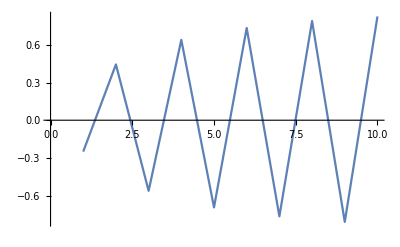

```mathematica
ListLinePlot[function[Range[10]]]
```

It fails the preliminary test.

sum of ((-1)^i i^2)/(i+1)^2 from i=1 to ∞

WolframAlphaQueryResults

## 5.5

```mathematica
∑_(i=1)^∞ (i!)/(i!+1)
```

Sum::div: Sum does not converge.

∑_(i=1)^∞ (i!)/(1+i!)

```mathematica
function=i↦(i!)/(i!+1);
```

```mathematica
function[Range[20]]
```

{1/2,2/3,6/7,24/25,120/121,720/721,5040/5041,40320/40321,362880/362881,3628800/3628801,39916800/39916801,479001600/479001601,6227020800/6227020801,87178291200/87178291201,1307674368000/1307674368001,20922789888000/20922789888001,355687428096000/355687428096001,6402373705728000/6402373705728001,121645100408832000/121645100408832001,2432902008176640000/2432902008176640001}

```mathematica
Limit[function[i],{i->∞}]
```

1

```mathematica
Limit[function[i],{i->∞}]!=0
```

True

The function fails the preliminary test.

sum of (i!)/(i!+1) from i=1 to infinity

WolframAlphaQueryResults

## 5.6

```mathematica
∑_(i=1)^∞ (i!)/((i+1)!)
```

Sum::div: Sum does not converge.

∑_(i=1)^∞ (i!)/((1+i)!)

```mathematica
function=i↦(i!)/((i+1)!);
```

```mathematica
Limit[function[i],i->∞]
```

0

More testing is needed.

## 5.8

```mathematica
function=i↦Log[i]/i;
```

```mathematica
Limit[function[i],i->∞]
```

0

More testing is needed.

## 5.9

```mathematica
function=3^#/(2^#+3^#)&
```

3^#1/(2^#1+3^#1)&

```mathematica
Limit[function[n],n->∞]
```

1

The series does not converge.